```mathematica
SetDirectory[NotebookDirectory[]];
<< Italy2018ElectionDataAnalysis.wl;
SetOptions[$FrontEndSession,{DynamicEvaluationTimeout->20.}] (*Set del timeout per ShowInterface2Interactive*)
```

```mathematica
LoadDataByYear["2018"];
```

Loading the 2018 Chamber of Deputies dataset from cache...

...loaded!

Loading the 2018 Senate of the Republic dataset from cache...

...loaded!

```mathematica
Le successive 3 istruzioni generano l'interfaccia.
```

```mathematica
(*ShowInterface1[]*)
```

```mathematica
(*ShowInterface2Interactive[]*)
```

```mathematica
ShowInterface3[]
```

```mathematica
GetCandidate["luigi", "di maio"]
```

{03 - ACERRA,,,}

# Dati e funzioni di test

```mathematica
ChamberOfDeputies
```

Chamber of Deputies

```mathematica
SenateOfTheRepublic
```

Senate of the Republic

```mathematica
PlottingElectionElectorsPie[ChamberOfDeputies]
```

-Graphics-

```mathematica
PlottingElectionElectorsPie[SenateOfTheRepublic]
```

-Graphics-

```mathematica
PlottingElectionVotersPie[ChamberOfDeputies, query->"ELETTORI = 13746"]
```

-Graphics-

```mathematica
PlottingElectionVotersNonVotersPie[ChamberOfDeputies]
```

-Graphics-

```mathematica
PlottingElectionVotersNonVotersPie[SenateOfTheRepublic]
```

-Graphics-

Part::pkspec1: The expression Italy2018ElectionDataAnalysis`Private`selectedYear cannot be used as a part specification.

Part::pspec1: Part specification Sinistra is not applicable.

Part::pkspec1: The expression Italy2018ElectionDataAnalysis`Private`selectedYear cannot be used as a part specification.

Part::pspec1: Part specification district is not applicable.

Part::pkspec1: The expression Italy2018ElectionDataAnalysis`Private`selectedYear cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::pspec1: Part specification list is not applicable.

General::stop: Further output of Part::pspec1 will be suppressed during this calculation.

GeoRegionValuePlot::ldata: {{Abruzzes, Italy,Total[Italy2018ElectionDataAnalysis`Private`chamberDataset[Select[MemberQ[Italy2018ElectionDataAnalysis`Private`parties$13965,Slot[«1»][«1»]]&]][Select[Italy2018ElectionDataAnalysis`Private`GetRegionFromDistrict[«1»]==Italy2018ElectionDataAnalysis`Private`r&]][All,<|2018→<|district→CIRCOSCRIZIONE,province→PROVINCIA,lastname→COGNOME,«7»,list→LISTA,singleMemberDistrict→UNINOMINALE,singleMemberDistrictCandidateOnlyVotes→VOTISOLOCANDUNINOM|>|>⟦«50»⟧⟦singleM…ateVotes⟧]]},«9»,«10»} is not a valid dataset or list of datasets.

GeoRegionValuePlot::ldata: {{Abruzzes, Italy,Total[Italy2018ElectionDataAnalysis`Private`chamberDataset[Select[MemberQ[Italy2018ElectionDataAnalysis`Private`parties$13983,Slot[«1»][«1»]]&]][Select[Italy2018ElectionDataAnalysis`Private`GetRegionFromDistrict[«1»]==Italy2018ElectionDataAnalysis`Private`r&]][All,<|2018→<|district→CIRCOSCRIZIONE,province→PROVINCIA,lastname→COGNOME,«7»,list→LISTA,singleMemberDistrict→UNINOMINALE,singleMemberDistrictCandidateOnlyVotes→VOTISOLOCANDUNINOM|>|>⟦«50»⟧⟦singleM…ateVotes⟧]]},«9»,«10»} is not a valid dataset or list of datasets.

GeoRegionValuePlot::ldata: {{Abruzzes, Italy,Total[Italy2018ElectionDataAnalysis`Private`chamberDataset[Select[MemberQ[Italy2018ElectionDataAnalysis`Private`parties$13985,Slot[«1»][«1»]]&]][Select[Italy2018ElectionDataAnalysis`Private`GetRegionFromDistrict[«1»]==Italy2018ElectionDataAnalysis`Private`r&]][All,<|2018→<|district→CIRCOSCRIZIONE,province→PROVINCIA,lastname→COGNOME,«7»,list→LISTA,singleMemberDistrict→UNINOMINALE,singleMemberDistrictCandidateOnlyVotes→VOTISOLOCANDUNINOM|>|>⟦«50»⟧⟦singleM…ateVotes⟧]]},«9»,«10»} is not a valid dataset or list of datasets.

General::stop: Further output of GeoRegionValuePlot::ldata will be suppressed during this calculation.

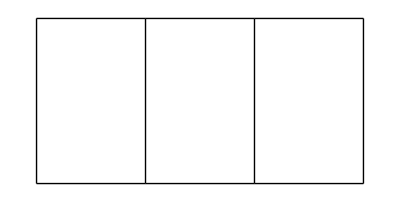

```mathematica
PlottingElectionRegionCoalitionsBars[ChamberOfDeputies]
```

```mathematica
PlottingElectionRegionCoalitionsBars[SenateOfTheRepublic]
```

-Graphics-

```mathematica
PlottingElectionRegionCoalitionsBars3D[ChamberOfDeputies]
```

Exporting 3D models...

...Exported all file!

```mathematica
PlottingElectionRegionCoalitionsBars3D[SenateOfTheRepublic]
```

Exporting 3D models...

...Exported all file!

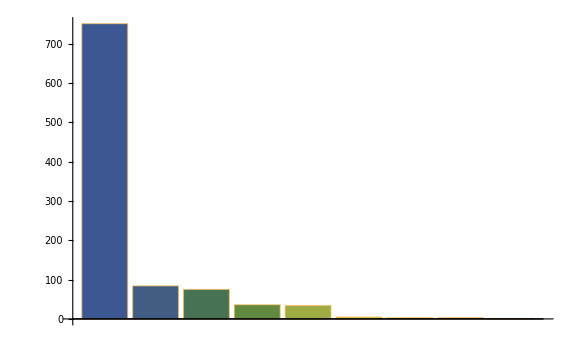

```mathematica
luigidimaio=PlottingCandidate["luigi", "di maio",city->"pomigliano d'arco"]
```

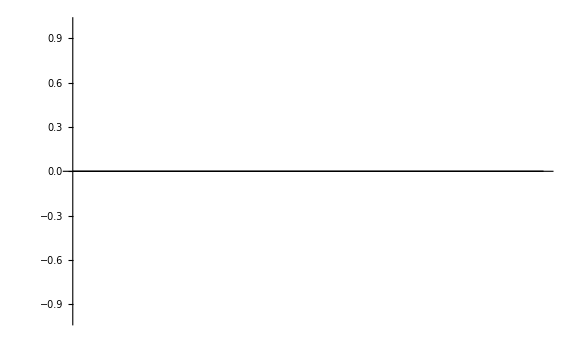

```mathematica
notfound = PlottingCandidate["tommaso","azzalin"]
```

```mathematica
PlottingRegionsItalyMap[]
```

Exporting the image...

...Exported the image!